# Twine HTML Parser

```mathematica
Clear[twineParser]
```

```mathematica
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
```

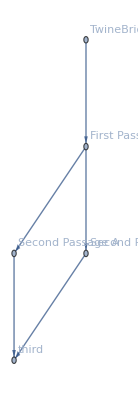

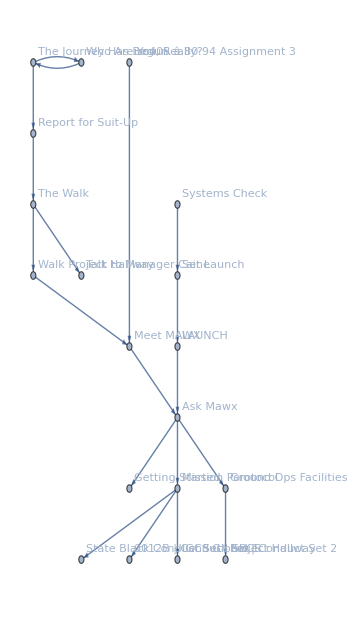

```mathematica
twineParser[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,edges,alledges, g, v},
(*Import Twine Project as string*)
fileAsString = Import[absoluteFilePath, "String"];
(*Explicitly Parse XML | Riccardo's Algorithm*)
xmlObject = parseXML[fileAsString];
(*Get the root node*)
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
(*Extract the Story name*)
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
(*Extract the passages in the form {passage-name, content}*)
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
(*Create Assocation between passage and content for tooltips*)
 passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
(*Add rootnode pair to association*)
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
(*Extract Links*)
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
(*generate edges*)
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
(*create complete list of edges for graph*)
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
(*Generate Graph*)
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}]
]
test=twineParser["~/Documents/Twine/Stories/TwineBridge_Test.html"]
test2 = twineParser["~/Documents/Twine/Stories/isc405 _ Assignment 3.html"]
```

#### With Echo Statements

```mathematica
Clear[twineParser2]
twineParser2[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,edges,rules},
(*Import Twine Project as string*)
fileAsString = Import[absoluteFilePath, "String"];
(*Explicitly Parse XML | Riccardo's Algorithm*)
xmlObject = parseXML[fileAsString];
(*Get the root node*)
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
(*Extract the Story name*)
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
Echo[rootNodeName, "STORY NAME: "];
(*Extract the passages in the form {passage-name, content}*)
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,Echo[content,"CONTENT: "]}, {0, Infinity}];
(*Extract Links*)
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[Echo[#⟦1⟧, "Passage Names : "], extractLinks[#⟦2⟧]]&/@passages;
rules= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
Graph[rules, VertexLabels->"Name", GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}]
]
```

#### XML Parser | Riccardo

```mathematica
$tag =(WordCharacter|"-")..

parseAttrs[expr_String] := Cases[
StringReplace[
expr,{
k:$tag~~"=\"" ~~ v:Shortest[___] ~~ "\"" :> {k -> v},
k:$tag~~"='" ~~ v:Shortest[___] ~~ "'" :> {k -> v},
k:$tag~~"=" ~~ v:$tag :> {k -> v},
k:$tag :> {k -> ""}
}
],
_Rule,
All
]

parseXML[expr_String] := Quiet[
List @@ StringReplace[
expr,
{"<" ~~ tag:$tag ~~ attrs:Shortest[___] ~~ ">" ~~ body:Shortest[___] ~~ "</" ~~ tag:$tag ~~ ">" :> XMLElement[tag, parseAttrs @ attrs, parseXML@body],
"<" ~~ tag:$tag ~~ attrs:Shortest[___] ~~ "/>" :> XMLElement[tag, parseAttrs @ attrs, {}]
}
],
StringExpression::cond
]
```

(WordCharacter|-)..

```mathematica
xml =Import["~/Documents/Twine/Stories/TwineBridge_Test.html", "String"]
```

<tw-storydata name="TwineBridge_Test" startnode="1" creator="Twine" creator-version="2.2.1" ifid="579B2F48-823C-46E0-9C6C-AC01FFDA9A56" zoom="1" format="Harlowe" format-version="2.1.0" options="">
  <tw-passagedata pid="1" name="First Passage" tags="" position="320,377" size="100,100">
    This is my first passage. Now I&#39;ll go to one of two second passages [[Second Passage A]] [[Second Passage B]]</tw-passagedata>
  <tw-passagedata pid="2" name="Second Passage A" tags="" position="210,527" size="100,100">Go to the [[third]] passage</tw-passagedata>
  <tw-passagedata pid="3" name="Second Passage B" tags="" position="450,527" size="100,100">Go to the [[third]] passage</tw-passagedata>
  <tw-passagedata pid="4" name="third" tags="" position="318,686" size="100,100">Double-click this passage to edit it.</tw-passagedata>
</tw-storydata>

#### Separate Test

```mathematica
pxml =parseXML[xml];
```

```mathematica
rNode = Cases[pxml, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
```

```mathematica
psgs = Cases[rNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,Echo[content,"CONTENT: "]}, {0, Infinity}]
```

CONTENT:  
    This is my first passage. Now I&#39;ll go to one of two second passages [[Second Passage A]] [[Second Passage B]]

CONTENT:  Go to the [[third]] passage

CONTENT:  Go to the [[third]] passage

CONTENT:  Double-click this passage to edit it.

{{First Passage,
    This is my first passage. Now I&#39;ll go to one of two second passages [[Second Passage A]] [[Second Passage B]]},{Second Passage A,Go to the [[third]] passage},{Second Passage B,Go to the [[third]] passage},{third,Double-click this passage to edit it.}}

#### Generate Edges Test

From { PassageName , PassageContent } To Parent → Link_1, ... Parent → Link_n

```mathematica
Clear[generateEdges]
generatedEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
```

Use StringContainsQ or SringCases

```mathematica
StringCases["string [[link]]", StartOfString ~~ ___ ~~"[["~~passageName___~~"]]"~~___~~EndOfString:> passageName]
```

{link}

```mathematica
DeleteCases[StringCases[{"string [[link]]","other string [[other link]]", "hello [[this]] [[that]]", "there"},("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

{{link},{other link},{this,that}}

```mathematica
StringCases[{"string [[link]]","other string [[other link]]", "hello [[this]] [[that]]", "there"},("[["~~ShortestMatch[p___]~~"]]"):> p]
```

{{link},{other link},{this,that},{}}

```mathematica
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
extractLinks["this is my passage. Here is link [[one]] and here is link [[two]]"]
```

{one,two}

```mathematica
Thread[Rule[root, %302]]
```

{root→one,root→two}

```mathematica
Thread[DirectedEdge[root, %302]]
```

{root->one,root->two}

```mathematica
?StringContainsQ
```

StringContainsQ[string,patt] yields True if any part of string matches the string pattern patt, and yields False otherwise.
StringContainsQ[{string_1,string_2,…},patt] gives a list of the results for each of the string_i.
StringContainsQ[patt] represents an operator form of StringContainsQ that can be applied to an expression.